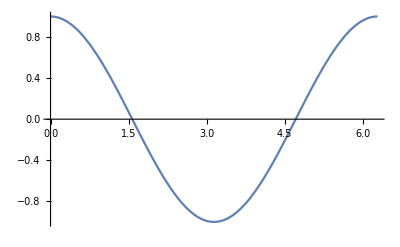

```mathematica
Plot[Cos[x],{x,0,2 π}]
```

```mathematica
f[x]:=Sin[x];
```

```mathematica
Manipulate[
Plot[{Cos[x],(Sin[x+delta]-Sin[x])/delta},{x,0,2 Pi}]
,{delta,1,0}]
```

```mathematica
testTable=Table[{i,j},{i,1,10},{j,1,10}]
```

{{{1,1},{1,2},{1,3},{1,4},{1,5},{1,6},{1,7},{1,8},{1,9},{1,10}},{{2,1},{2,2},{2,3},{2,4},{2,5},{2,6},{2,7},{2,8},{2,9},{2,10}},{{3,1},{3,2},{3,3},{3,4},{3,5},{3,6},{3,7},{3,8},{3,9},{3,10}},{{4,1},{4,2},{4,3},{4,4},{4,5},{4,6},{4,7},{4,8},{4,9},{4,10}},{{5,1},{5,2},{5,3},{5,4},{5,5},{5,6},{5,7},{5,8},{5,9},{5,10}},{{6,1},{6,2},{6,3},{6,4},{6,5},{6,6},{6,7},{6,8},{6,9},{6,10}},{{7,1},{7,2},{7,3},{7,4},{7,5},{7,6},{7,7},{7,8},{7,9},{7,10}},{{8,1},{8,2},{8,3},{8,4},{8,5},{8,6},{8,7},{8,8},{8,9},{8,10}},{{9,1},{9,2},{9,3},{9,4},{9,5},{9,6},{9,7},{9,8},{9,9},{9,10}},{{10,1},{10,2},{10,3},{10,4},{10,5},{10,6},{10,7},{10,8},{10,9},{10,10}}}

```mathematica
Manipulate[
ListPlot[testTable[[k]]],{k,1,10,1}
]
```

```mathematica
p[x_]:=x^6-8 x^5+19 x^4-49 x^2+24 x+45;
reg=ImplicitRegion[x^2+y^2≤E^2,{x,y}]
```

ImplicitRegion[x^2+y^2≤ⅇ^2,{x,y}]

```mathematica
NIntegrate[p[x] Cos[x+y],{x,y}∈reg]
```

-957.337

```mathematica
Maximize[{-2x^2-3x+5,-5≤x≤5},x]//N
```

{6.125,{x→-0.75}}

```mathematica
FindMinimum[x Cos[x],x,MaxIterations->10]
```

FindMinimum::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

{-3.28837,{x→3.42562}}

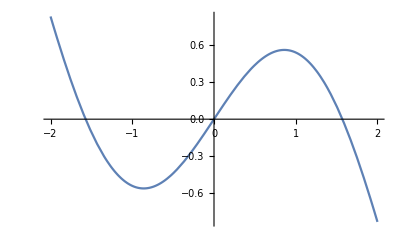

```mathematica
Plot[x Cos[x],{x,-2,2}]
```

```mathematica
matrix=Table[i+j,{i,-6,5},{j,-6,5}]
```

{{-12,-11,-10,-9,-8,-7,-6,-5,-4,-3,-2,-1},{-11,-10,-9,-8,-7,-6,-5,-4,-3,-2,-1,0},{-10,-9,-8,-7,-6,-5,-4,-3,-2,-1,0,1},{-9,-8,-7,-6,-5,-4,-3,-2,-1,0,1,2},{-8,-7,-6,-5,-4,-3,-2,-1,0,1,2,3},{-7,-6,-5,-4,-3,-2,-1,0,1,2,3,4},{-6,-5,-4,-3,-2,-1,0,1,2,3,4,5},{-5,-4,-3,-2,-1,0,1,2,3,4,5,6},{-4,-3,-2,-1,0,1,2,3,4,5,6,7},{-3,-2,-1,0,1,2,3,4,5,6,7,8},{-2,-1,0,1,2,3,4,5,6,7,8,9},{-1,0,1,2,3,4,5,6,7,8,9,10}}

```mathematica
matrix//Dimensions
```

{12,12}

```mathematica
matrix//Dimensions//Length
```

2

```mathematica
matrix2=Table[2 i+3 j,{i,1,12},{j,1,12}]
```

{{5,8,11,14,17,20,23,26,29,32,35,38},{7,10,13,16,19,22,25,28,31,34,37,40},{9,12,15,18,21,24,27,30,33,36,39,42},{11,14,17,20,23,26,29,32,35,38,41,44},{13,16,19,22,25,28,31,34,37,40,43,46},{15,18,21,24,27,30,33,36,39,42,45,48},{17,20,23,26,29,32,35,38,41,44,47,50},{19,22,25,28,31,34,37,40,43,46,49,52},{21,24,27,30,33,36,39,42,45,48,51,54},{23,26,29,32,35,38,41,44,47,50,53,56},{25,28,31,34,37,40,43,46,49,52,55,58},{27,30,33,36,39,42,45,48,51,54,57,60}}

```mathematica
matrix*matrix2
```

{{-60,-88,-110,-126,-136,-140,-138,-130,-116,-96,-70,-38},{-77,-100,-117,-128,-133,-132,-125,-112,-93,-68,-37,0},{-90,-108,-120,-126,-126,-120,-108,-90,-66,-36,0,42},{-99,-112,-119,-120,-115,-104,-87,-64,-35,0,41,88},{-104,-112,-114,-110,-100,-84,-62,-34,0,40,86,138},{-105,-108,-105,-96,-81,-60,-33,0,39,84,135,192},{-102,-100,-92,-78,-58,-32,0,38,82,132,188,250},{-95,-88,-75,-56,-31,0,37,80,129,184,245,312},{-84,-72,-54,-30,0,36,78,126,180,240,306,378},{-69,-52,-29,0,35,76,123,176,235,300,371,448},{-50,-28,0,34,74,120,172,230,294,364,440,522},{-27,0,33,72,117,168,225,288,357,432,513,600}}

```mathematica
Dot[matrix,matrix2]
```

{{-962,-1196,-1430,-1664,-1898,-2132,-2366,-2600,-2834,-3068,-3302,-3536},{-770,-968,-1166,-1364,-1562,-1760,-1958,-2156,-2354,-2552,-2750,-2948},{-578,-740,-902,-1064,-1226,-1388,-1550,-1712,-1874,-2036,-2198,-2360},{-386,-512,-638,-764,-890,-1016,-1142,-1268,-1394,-1520,-1646,-1772},{-194,-284,-374,-464,-554,-644,-734,-824,-914,-1004,-1094,-1184},{-2,-56,-110,-164,-218,-272,-326,-380,-434,-488,-542,-596},{190,172,154,136,118,100,82,64,46,28,10,-8},{382,400,418,436,454,472,490,508,526,544,562,580},{574,628,682,736,790,844,898,952,1006,1060,1114,1168},{766,856,946,1036,1126,1216,1306,1396,1486,1576,1666,1756},{958,1084,1210,1336,1462,1588,1714,1840,1966,2092,2218,2344},{1150,1312,1474,1636,1798,1960,2122,2284,2446,2608,2770,2932}}

```mathematica
Inverse[matrix.matrix2]
```

Inverse::sing: Matrix … is singular.

Inverse[{{-962,-1196,-1430,-1664,-1898,-2132,-2366,-2600,-2834,-3068,-3302,-3536},{-770,-968,-1166,-1364,-1562,-1760,-1958,-2156,-2354,-2552,-2750,-2948},{-578,-740,-902,-1064,-1226,-1388,-1550,-1712,-1874,-2036,-2198,-2360},{-386,-512,-638,-764,-890,-1016,-1142,-1268,-1394,-1520,-1646,-1772},{-194,-284,-374,-464,-554,-644,-734,-824,-914,-1004,-1094,-1184},{-2,-56,-110,-164,-218,-272,-326,-380,-434,-488,-542,-596},{190,172,154,136,118,100,82,64,46,28,10,-8},{382,400,418,436,454,472,490,508,526,544,562,580},{574,628,682,736,790,844,898,952,1006,1060,1114,1168},{766,856,946,1036,1126,1216,1306,1396,1486,1576,1666,1756},{958,1084,1210,1336,1462,1588,1714,1840,1966,2092,2218,2344},{1150,1312,1474,1636,1798,1960,2122,2284,2446,2608,2770,2932}}]

```mathematica
IdentityMatrix[10]//MatrixForm
```

(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1)

```mathematica
Transpose[matrix.matrix2]
```

{{-962,-770,-578,-386,-194,-2,190,382,574,766,958,1150},{-1196,-968,-740,-512,-284,-56,172,400,628,856,1084,1312},{-1430,-1166,-902,-638,-374,-110,154,418,682,946,1210,1474},{-1664,-1364,-1064,-764,-464,-164,136,436,736,1036,1336,1636},{-1898,-1562,-1226,-890,-554,-218,118,454,790,1126,1462,1798},{-2132,-1760,-1388,-1016,-644,-272,100,472,844,1216,1588,1960},{-2366,-1958,-1550,-1142,-734,-326,82,490,898,1306,1714,2122},{-2600,-2156,-1712,-1268,-824,-380,64,508,952,1396,1840,2284},{-2834,-2354,-1874,-1394,-914,-434,46,526,1006,1486,1966,2446},{-3068,-2552,-2036,-1520,-1004,-488,28,544,1060,1576,2092,2608},{-3302,-2750,-2198,-1646,-1094,-542,10,562,1114,1666,2218,2770},{-3536,-2948,-2360,-1772,-1184,-596,-8,580,1168,1756,2344,2932}}

```mathematica
solution=Solve[x^2+y^2≤64,Integers];
```

```mathematica
Reduce[x^2+y^2≤64,Integers]
```

(x==-8&&y==0)||(x==-7&&y==-3)||(x==-7&&y==-2)||(x==-7&&y==-1)||(x==-7&&y==0)||(x==-7&&y==1)||(x==-7&&y==2)||(x==-7&&y==3)||(x==-6&&y==-5)||(x==-6&&y==-4)||(x==-6&&y==-3)||(x==-6&&y==-2)||(x==-6&&y==-1)||(x==-6&&y==0)||(x==-6&&y==1)||(x==-6&&y==2)||(x==-6&&y==3)||(x==-6&&y==4)||(x==-6&&y==5)||(x==-5&&y==-6)||(x==-5&&y==-5)||(x==-5&&y==-4)||(x==-5&&y==-3)||(x==-5&&y==-2)||(x==-5&&y==-1)||(x==-5&&y==0)||(x==-5&&y==1)||(x==-5&&y==2)||(x==-5&&y==3)||(x==-5&&y==4)||(x==-5&&y==5)||(x==-5&&y==6)||(x==-4&&y==-6)||(x==-4&&y==-5)||(x==-4&&y==-4)||(x==-4&&y==-3)||(x==-4&&y==-2)||(x==-4&&y==-1)||(x==-4&&y==0)||(x==-4&&y==1)||(x==-4&&y==2)||(x==-4&&y==3)||(x==-4&&y==4)||(x==-4&&y==5)||(x==-4&&y==6)||(x==-3&&y==-7)||(x==-3&&y==-6)||(x==-3&&y==-5)||(x==-3&&y==-4)||(x==-3&&y==-3)||(x==-3&&y==-2)||(x==-3&&y==-1)||(x==-3&&y==0)||(x==-3&&y==1)||(x==-3&&y==2)||(x==-3&&y==3)||(x==-3&&y==4)||(x==-3&&y==5)||(x==-3&&y==6)||(x==-3&&y==7)||(x==-2&&y==-7)||(x==-2&&y==-6)||(x==-2&&y==-5)||(x==-2&&y==-4)||(x==-2&&y==-3)||(x==-2&&y==-2)||(x==-2&&y==-1)||(x==-2&&y==0)||(x==-2&&y==1)||(x==-2&&y==2)||(x==-2&&y==3)||(x==-2&&y==4)||(x==-2&&y==5)||(x==-2&&y==6)||(x==-2&&y==7)||(x==-1&&y==-7)||(x==-1&&y==-6)||(x==-1&&y==-5)||(x==-1&&y==-4)||(x==-1&&y==-3)||(x==-1&&y==-2)||(x==-1&&y==-1)||(x==-1&&y==0)||(x==-1&&y==1)||(x==-1&&y==2)||(x==-1&&y==3)||(x==-1&&y==4)||(x==-1&&y==5)||(x==-1&&y==6)||(x==-1&&y==7)||(x==0&&y==-8)||(x==0&&y==-7)||(x==0&&y==-6)||(x==0&&y==-5)||(x==0&&y==-4)||(x==0&&y==-3)||(x==0&&y==-2)||(x==0&&y==-1)||(x==0&&y==0)||(x==0&&y==1)||(x==0&&y==2)||(x==0&&y==3)||(x==0&&y==4)||(x==0&&y==5)||(x==0&&y==6)||(x==0&&y==7)||(x==0&&y==8)||(x==1&&y==-7)||(x==1&&y==-6)||(x==1&&y==-5)||(x==1&&y==-4)||(x==1&&y==-3)||(x==1&&y==-2)||(x==1&&y==-1)||(x==1&&y==0)||(x==1&&y==1)||(x==1&&y==2)||(x==1&&y==3)||(x==1&&y==4)||(x==1&&y==5)||(x==1&&y==6)||(x==1&&y==7)||(x==2&&y==-7)||(x==2&&y==-6)||(x==2&&y==-5)||(x==2&&y==-4)||(x==2&&y==-3)||(x==2&&y==-2)||(x==2&&y==-1)||(x==2&&y==0)||(x==2&&y==1)||(x==2&&y==2)||(x==2&&y==3)||(x==2&&y==4)||(x==2&&y==5)||(x==2&&y==6)||(x==2&&y==7)||(x==3&&y==-7)||(x==3&&y==-6)||(x==3&&y==-5)||(x==3&&y==-4)||(x==3&&y==-3)||(x==3&&y==-2)||(x==3&&y==-1)||(x==3&&y==0)||(x==3&&y==1)||(x==3&&y==2)||(x==3&&y==3)||(x==3&&y==4)||(x==3&&y==5)||(x==3&&y==6)||(x==3&&y==7)||(x==4&&y==-6)||(x==4&&y==-5)||(x==4&&y==-4)||(x==4&&y==-3)||(x==4&&y==-2)||(x==4&&y==-1)||(x==4&&y==0)||(x==4&&y==1)||(x==4&&y==2)||(x==4&&y==3)||(x==4&&y==4)||(x==4&&y==5)||(x==4&&y==6)||(x==5&&y==-6)||(x==5&&y==-5)||(x==5&&y==-4)||(x==5&&y==-3)||(x==5&&y==-2)||(x==5&&y==-1)||(x==5&&y==0)||(x==5&&y==1)||(x==5&&y==2)||(x==5&&y==3)||(x==5&&y==4)||(x==5&&y==5)||(x==5&&y==6)||(x==6&&y==-5)||(x==6&&y==-4)||(x==6&&y==-3)||(x==6&&y==-2)||(x==6&&y==-1)||(x==6&&y==0)||(x==6&&y==1)||(x==6&&y==2)||(x==6&&y==3)||(x==6&&y==4)||(x==6&&y==5)||(x==7&&y==-3)||(x==7&&y==-2)||(x==7&&y==-1)||(x==7&&y==0)||(x==7&&y==1)||(x==7&&y==2)||(x==7&&y==3)||(x==8&&y==0)

```mathematica
{x,y}/.{x->5,y->10}
```

{5,10}

```mathematica
coords={x,y}/.solution;
```

```mathematica
Solve[x^2+y^2≤64&&x≤5&&y≤5,Integers]
```

{{x→-8,y→0},{x→-7,y→-3},{x→-7,y→-2},{x→-7,y→-1},{x→-7,y→0},{x→-7,y→1},{x→-7,y→2},{x→-7,y→3},{x→-6,y→-5},{x→-6,y→-4},{x→-6,y→-3},{x→-6,y→-2},{x→-6,y→-1},{x→-6,y→0},{x→-6,y→1},{x→-6,y→2},{x→-6,y→3},{x→-6,y→4},{x→-6,y→5},{x→-5,y→-6},{x→-5,y→-5},{x→-5,y→-4},{x→-5,y→-3},{x→-5,y→-2},{x→-5,y→-1},{x→-5,y→0},{x→-5,y→1},{x→-5,y→2},{x→-5,y→3},{x→-5,y→4},{x→-5,y→5},{x→-4,y→-6},{x→-4,y→-5},{x→-4,y→-4},{x→-4,y→-3},{x→-4,y→-2},{x→-4,y→-1},{x→-4,y→0},{x→-4,y→1},{x→-4,y→2},{x→-4,y→3},{x→-4,y→4},{x→-4,y→5},{x→-3,y→-7},{x→-3,y→-6},{x→-3,y→-5},{x→-3,y→-4},{x→-3,y→-3},{x→-3,y→-2},{x→-3,y→-1},{x→-3,y→0},{x→-3,y→1},{x→-3,y→2},{x→-3,y→3},{x→-3,y→4},{x→-3,y→5},{x→-2,y→-7},{x→-2,y→-6},{x→-2,y→-5},{x→-2,y→-4},{x→-2,y→-3},{x→-2,y→-2},{x→-2,y→-1},{x→-2,y→0},{x→-2,y→1},{x→-2,y→2},{x→-2,y→3},{x→-2,y→4},{x→-2,y→5},{x→-1,y→-7},{x→-1,y→-6},{x→-1,y→-5},{x→-1,y→-4},{x→-1,y→-3},{x→-1,y→-2},{x→-1,y→-1},{x→-1,y→0},{x→-1,y→1},{x→-1,y→2},{x→-1,y→3},{x→-1,y→4},{x→-1,y→5},{x→0,y→-8},{x→0,y→-7},{x→0,y→-6},{x→0,y→-5},{x→0,y→-4},{x→0,y→-3},{x→0,y→-2},{x→0,y→-1},{x→0,y→0},{x→0,y→1},{x→0,y→2},{x→0,y→3},{x→0,y→4},{x→0,y→5},{x→1,y→-7},{x→1,y→-6},{x→1,y→-5},{x→1,y→-4},{x→1,y→-3},{x→1,y→-2},{x→1,y→-1},{x→1,y→0},{x→1,y→1},{x→1,y→2},{x→1,y→3},{x→1,y→4},{x→1,y→5},{x→2,y→-7},{x→2,y→-6},{x→2,y→-5},{x→2,y→-4},{x→2,y→-3},{x→2,y→-2},{x→2,y→-1},{x→2,y→0},{x→2,y→1},{x→2,y→2},{x→2,y→3},{x→2,y→4},{x→2,y→5},{x→3,y→-7},{x→3,y→-6},{x→3,y→-5},{x→3,y→-4},{x→3,y→-3},{x→3,y→-2},{x→3,y→-1},{x→3,y→0},{x→3,y→1},{x→3,y→2},{x→3,y→3},{x→3,y→4},{x→3,y→5},{x→4,y→-6},{x→4,y→-5},{x→4,y→-4},{x→4,y→-3},{x→4,y→-2},{x→4,y→-1},{x→4,y→0},{x→4,y→1},{x→4,y→2},{x→4,y→3},{x→4,y→4},{x→4,y→5},{x→5,y→-6},{x→5,y→-5},{x→5,y→-4},{x→5,y→-3},{x→5,y→-2},{x→5,y→-1},{x→5,y→0},{x→5,y→1},{x→5,y→2},{x→5,y→3},{x→5,y→4},{x→5,y→5}}

```mathematica
For[i=1,i≤Length[coords],i++,
If[PrimeQ[coords[[i,1]]]&&PrimeQ[coords[[i,2]]],Print[coords[[i]]]]
]
```

{-7,-3}

{-7,-2}

{-7,2}

{-7,3}

{-5,-5}

{-5,-3}

{-5,-2}

{-5,2}

{-5,3}

{-5,5}

{-3,-7}

{-3,-5}

{-3,-3}

{-3,-2}

{-3,2}

{-3,3}

{-3,5}

{-3,7}

{-2,-7}

{-2,-5}

{-2,-3}

{-2,-2}

{-2,2}

{-2,3}

{-2,5}

{-2,7}

{2,-7}

{2,-5}

{2,-3}

{2,-2}

{2,2}

{2,3}

{2,5}

{2,7}

{3,-7}

{3,-5}

{3,-3}

{3,-2}

{3,2}

{3,3}

{3,5}

{3,7}

{5,-5}

{5,-3}

{5,-2}

{5,2}

{5,3}

{5,5}

{7,-3}

{7,-2}

{7,2}

{7,3}

```mathematica
For[i=1,i≤Length[coords],i++,
If[OddQ[coords[[i,1]]]&&OddQ[coords[[i,2]]],Print[coords[[i]]]]
]
```

{-7,-3}

{-7,-1}

{-7,1}

{-7,3}

{-5,-5}

{-5,-3}

{-5,-1}

{-5,1}

{-5,3}

{-5,5}

{-3,-7}

{-3,-5}

{-3,-3}

{-3,-1}

{-3,1}

{-3,3}

{-3,5}

{-3,7}

{-1,-7}

{-1,-5}

{-1,-3}

{-1,-1}

{-1,1}

{-1,3}

{-1,5}

{-1,7}

{1,-7}

{1,-5}

{1,-3}

{1,-1}

{1,1}

{1,3}

{1,5}

{1,7}

{3,-7}

{3,-5}

{3,-3}

{3,-1}

{3,1}

{3,3}

{3,5}

{3,7}

{5,-5}

{5,-3}

{5,-1}

{5,1}

{5,3}

{5,5}

{7,-3}

{7,-1}

{7,1}

{7,3}

```mathematica
Mod[15,3]
```

0